```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
```

```mathematica
tvaluedat={0.25,0.28,0.3,0.32,0.33,0.34,0.345,0.35,0.37,0.4,0.42};
datrotuwsoca=Table[Flatten[Import[StringJoin["trot_",ToString[tvalue],"_nutcalca.dat"]]],{tvalue,tvaluedat}];
datrotdwsoca=Table[Flatten[Import[StringJoin["trot_",ToString[tvalue],"_ndtcalca.dat"]]],{tvalue,tvaluedat}];
datrotuwsocb=Table[Flatten[Import[StringJoin["trot_",ToString[tvalue],"_nutcalcb.dat"]]],{tvalue,tvaluedat}];
datrotdwsocb=Table[Flatten[Import[StringJoin["trot_",ToString[tvalue],"_ndtcalcb.dat"]]],{tvalue,tvaluedat}];
```

```mathematica
occupationa=Table[Table[Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,1]] + Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,2]]+ Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,3]],{i,1,Nx*Ny}][[1]],{l,1,Length[tvaluedat]}];


occupationb=Table[Table[Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,1]] + Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,2]]+ Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,3]],{i,1,Nx*Ny}][[1]],{l,1,Length[tvaluedat]}];
```

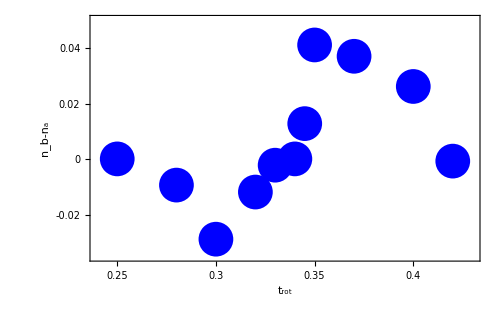

```mathematica
occudata=Take[Table[{tvaluedat[[i]],(occupationb-occupationa)[[i]]},{i,1,Length[tvaluedat]}],(Length[tvaluedat])];
crossingpt=6;
occuplot=ListPlot[occudata,Frame->True,FrameStyle->Directive[Thickness[0.005],Black,32],Epilog->{{Blue,PointSize[0.05],Point[Take[occudata,crossingpt]]},{Blue,PointSize[0.05],Point[Take[occudata,-(Length[occudata]-crossingpt)]]}},PlotRange->{{0.24,0.43},{-0.035,0.05}},
FrameTicks->{{{{-0.02,-0.02,0.03},{0,0,0.03},{0.02,0.02,0.03},{0.04,0.04,0.03}},{{-0.02,Null,0.03},{0,Null,0.03},{0.02,Null,0.03},{0.04,Null,0.03}}},{{{0.25,0.25,0.03},{0.3,0.3,0.03},{0.35,0.35,0.03},{0.4,0.4,0.03}},{{0.25,Null,0.03},{0.3,Null,0.03},{0.35,Null,0.03},{0.4,Null,0.03}}}},
FrameLabel->{{Style["n_b-n_a",35,FontFamily->"TimesNewRoman"],None},{Style["t_rot",35,FontFamily->"TimesNewRoman"],None}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,40]},ImagePadding->{{125,15},{90,17}},ImageSize->500]
Export["occuplot.eps",occuplot];
```